### Pr(t)=1/2+1/2 ⅇ^(-t/T_2)cos(c_4 t/T+c_3)

```mathematica
Pr={0.9384765625,0.8212890625,0.6728515625,0.4873046875,0.3486328125,0.2548828125,0.19140625,0.1767578125,0.2587890625,0.35546875,0.47265625,0.587890625,0.6865234375,0.7265625,0.76953125,0.7890625,0.720703125,0.658203125,0.57421875,0.5029296875,0.4287109375,0.3994140625,0.3740234375,0.345703125,0.3701171875,0.451171875,0.501953125,0.568359375,0.6162109375,0.626953125,0.6416015625,0.650390625,0.6328125,0.607421875,0.5751953125,0.529296875,0.486328125,0.462890625,0.4365234375,0.4296875,0.43359375,0.515625,0.5234375,0.5400390625,0.5751953125,0.5869140625,0.5859375,0.6123046875,0.5751953125,0.5751953125};
Ngates=Table[i,{i,1,50}];
```

```mathematica
PrN=Table[{Ngates⟦i⟧,Pr⟦i⟧},{i,50}];
```

```mathematica
f1=1/2+1/2 ⅇ^(-t/T2)Cos[ c4 t/T+c3];
```

```mathematica
fit1=NonlinearModelFit[PrN,f1,{c4,c3,T2,T},t]
```

FittedModel[1/2+1/2 ⅇ^(-0.0446051 t) Cos[0.0399519+0.398115 t]]

```mathematica
FindFit[PrN,f1,{c3,c4,T,T2},t]
```

{c3→0.0399519,c4→9.97453,T→25.0544,T2→22.419}

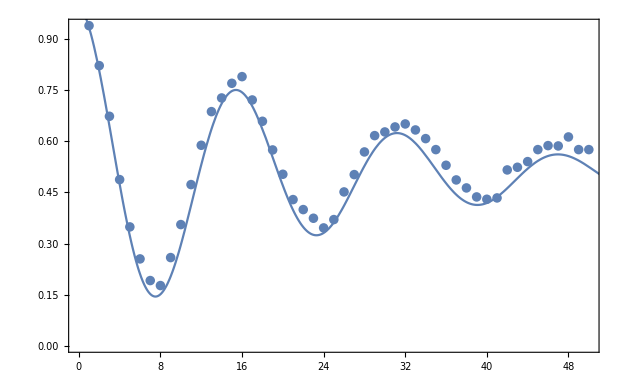

```mathematica
Show[ListPlot[PrN],Plot[fit1[t],{t,0,60}],Frame->True]
```

Error=1/N∑_(i=1)^N (f_1(i)-d(i))^2:

```mathematica
error1=fit1["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

0.0013933

```mathematica
f2=c1+c2 ⅇ^(-t/T2)Cos[ c4 t/T+c3];
```

```mathematica
fit2=NonlinearModelFit[PrN,f2,{c1,c2,c4,c3,T2,T},t]
```

FittedModel[0.535208+0.480626 ⅇ^(-«21» t) Cos[0.104305+0.394637 t]]

```mathematica
FindFit[PrN,f2,{c1,c2,c3,c4,T,T2},t]
```

{c1→0.535208,c2→0.480626,c3→0.104305,c4→5.2254,T→13.241,T2→23.2806}

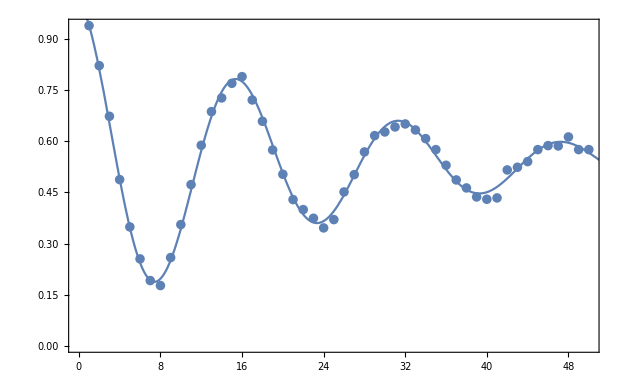

```mathematica
Show[ListPlot[PrN],Plot[fit2[t],{t,0,60}],Frame->True]
```

Error=1/N∑_(i=1)^N (f_1(i)-d(i))^2:

```mathematica
error2=fit2["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

0.000175564

```mathematica
5/13//N
```

0.384615

## Change Phase: phase=phase+k*np.pi/len(exp_vector)

```mathematica
(* The best backend is ibmqx2 *)
(* k=0,1,...11 *)
(* f2=c1+c2*ⅇ^(-t/T2)Cos[c4 t/T+c3] *)
```

```mathematica
Pr0={0.9482421875,0.9248046875,0.9296875,0.9033203125,0.87109375,0.8759765625,0.8583984375,0.8076171875,0.802734375,0.7802734375,0.7373046875,0.7255859375,0.69140625,0.681640625,0.6416015625,0.64453125,0.6357421875,0.6083984375,0.5732421875,0.544921875,0.5439453125,0.5537109375,0.5361328125,0.4931640625,0.505859375,0.5068359375,0.5234375,0.505859375,0.4970703125,0.4912109375,0.501953125,0.515625,0.5224609375,0.5234375,0.5283203125,0.5576171875,0.548828125,0.5673828125,0.576171875,0.587890625,0.5556640625,0.59765625,0.6025390625,0.6064453125,0.6171875,0.623046875,0.6015625,0.6376953125,0.66015625,0.65625};
PrN0=Table[{Ngates⟦i⟧,Pr0⟦i⟧},{i,50}];
fit0=NonlinearModelFit[PrN0,f2,{c1,c2,c4,c3,T2,T},t]
```

General::munfl: -0.0119782/(-1.53943416425022×10^1825) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00604592/(7.69717082125111×10^1824) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.26332×10^-6)/(-1.11578852469231×10^1619) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FittedModel[0.638633-0.0874888 ⅇ^(«1») Cos[0.608139+«19» t]]

```mathematica
FindFit[PrN0,f2,{c1,c2,c3,c4,T,T2},t]
```

General::munfl: -0.0119806/(-5.49040429424749×10^1829) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00604713/(2.74520214712375×10^1829) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.27966×10^-6)/(-2.18392651550566×10^1622) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{c1→0.638633,c2→-0.0871756,c3→0.60818,c4→0.818692,T→1.16777,T2→0.0166037}

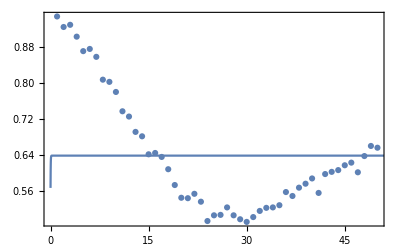

General::munfl: Exp[-743.934] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-783.089] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.243] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0174178

```mathematica
Show[ListPlot[PrN0],Plot[fit0[t],{t,0,60}],Frame->True]
fit0["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

General::munfl: -0.179614/(-4.18373156887477×10^435) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0912666/(2.09186578443739×10^435) is too small to represent as a normalized machine number; precision may be lost.

{c1→0.432755,c2→0.585871,c3→0.46483,c4→-0.0820448,T→1.44834,T2→26.4495}

General::munfl: -0.179606/(-5.87962077120257×10^434) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0912621/(2.93981038560128×10^434) is too small to represent as a normalized machine number; precision may be lost.

FittedModel[0.432755+0.585871 ⅇ^(«1») Cos[0.46483-«21» t]]

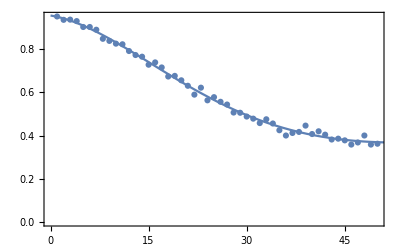

0.0001826

```mathematica
Pr1={0.9521484375,0.9365234375,0.9375,0.9306640625,0.9033203125,0.9033203125,0.890625,0.8486328125,0.8388671875,0.826171875,0.8232421875,0.7919921875,0.7734375,0.765625,0.728515625,0.7392578125,0.7158203125,0.673828125,0.6767578125,0.65625,0.630859375,0.58984375,0.6220703125,0.5634765625,0.578125,0.556640625,0.5439453125,0.5068359375,0.505859375,0.48828125,0.478515625,0.4580078125,0.4755859375,0.4560546875,0.4248046875,0.400390625,0.412109375,0.4169921875,0.4462890625,0.4072265625,0.419921875,0.404296875,0.3818359375,0.3857421875,0.3779296875,0.3583984375,0.3681640625,0.400390625,0.3583984375,0.3623046875};
PrN1=Table[{Ngates⟦i⟧,Pr1⟦i⟧},{i,50}];
FindFit[PrN1,f2,{c1,c2,c3,c4,T,T2},t]
fit1=NonlinearModelFit[PrN1,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN1],Plot[fit1[t],{t,0,60}],Frame->True]
fit1["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

```mathematica
Pr2={0.9521484375,0.9365234375,0.9375,0.9306640625,0.9033203125,0.9033203125,0.890625,0.8486328125,0.8388671875,0.826171875,0.8232421875,0.7919921875,0.7734375,0.765625,0.728515625,0.7392578125,0.7158203125,0.673828125,0.6767578125,0.65625,0.630859375,0.58984375,0.6220703125,0.5634765625,0.578125,0.556640625,0.5439453125,0.5068359375,0.505859375,0.48828125,0.478515625,0.4580078125,0.4755859375,0.4560546875,0.4248046875,0.400390625,0.412109375,0.4169921875,0.4462890625,0.4072265625,0.419921875,0.404296875,0.3818359375,0.3857421875,0.3779296875,0.3583984375,0.3681640625,0.400390625,0.3583984375,0.3623046875};
PrN2=Table[{Ngates⟦i⟧,Pr2⟦i⟧},{i,50}];
FindFit[PrN2,f2,{c1,c2,c3,c4,T,T2},t]
fit2=NonlinearModelFit[PrN2,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN2],Plot[fit2[t],{t,0,60}],Frame->True]
fit2["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

General::munfl: -0.179614/(-4.18373156887477×10^435) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0912666/(2.09186578443739×10^435) is too small to represent as a normalized machine number; precision may be lost.

{c1→0.432755,c2→0.585871,c3→0.46483,c4→-0.0820448,T→1.44834,T2→26.4495}

General::munfl: -0.179606/(-5.87962077120257×10^434) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0912621/(2.93981038560128×10^434) is too small to represent as a normalized machine number; precision may be lost.

FittedModel[0.432755+0.585871 ⅇ^(«1») Cos[0.46483-«21» t]]

-Graphics-

0.0001826

{c1→0.4608,c2→0.557222,c3→-0.65436,c4→0.167029,T→0.871809,T2→13.942}

FittedModel[0.4608+0.557222 ⅇ^(«1») Cos[0.65436-«20» t]]

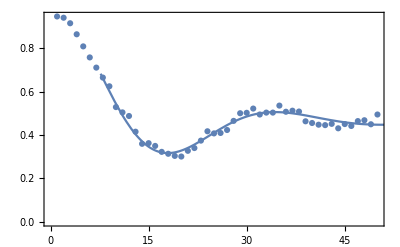

0.000390049

```mathematica
Pr3={0.9453125,0.939453125,0.9140625,0.86328125,0.8076171875,0.7568359375,0.7099609375,0.6640625,0.6240234375,0.5283203125,0.50390625,0.4873046875,0.4150390625,0.359375,0.3623046875,0.349609375,0.322265625,0.3134765625,0.3037109375,0.30078125,0.3271484375,0.33984375,0.3740234375,0.4169921875,0.4072265625,0.4091796875,0.4228515625,0.46484375,0.5,0.501953125,0.521484375,0.494140625,0.5029296875,0.5029296875,0.53515625,0.5068359375,0.51171875,0.5078125,0.462890625,0.455078125,0.447265625,0.4453125,0.451171875,0.4306640625,0.4501953125,0.44140625,0.4638671875,0.4677734375,0.44921875,0.494140625};
PrN3=Table[{Ngates⟦i⟧,Pr3⟦i⟧},{i,50}];
FindFit[PrN3,f2,{c1,c2,c3,c4,T,T2},t]
fit3=NonlinearModelFit[PrN3,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN3],Plot[fit3[t],{t,0,60}],Frame->True]
fit3["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

{c1→0.526896,c2→0.571912,c3→-0.184712,c4→2.1971,T→-11.0417,T2→16.8984}

FittedModel[0.526896+0.571912 ⅇ^(«1») Cos[0.184712+«20» t]]

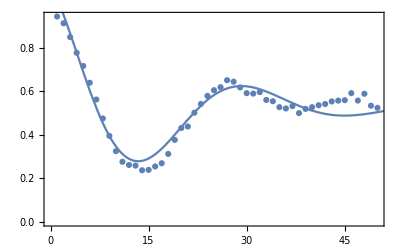

0.00174215

```mathematica
Pr4={0.9443359375,0.9130859375,0.849609375,0.77734375,0.716796875,0.6396484375,0.5625,0.4755859375,0.3955078125,0.3251953125,0.2763671875,0.26171875,0.2587890625,0.2373046875,0.2392578125,0.2548828125,0.26953125,0.3125,0.376953125,0.431640625,0.4384765625,0.501953125,0.5419921875,0.5791015625,0.60546875,0.619140625,0.6513671875,0.64453125,0.6181640625,0.591796875,0.58984375,0.5966796875,0.560546875,0.5546875,0.52734375,0.521484375,0.5322265625,0.5,0.51953125,0.52734375,0.5361328125,0.5419921875,0.5537109375,0.5576171875,0.5595703125,0.591796875,0.5576171875,0.5888671875,0.5341796875,0.5244140625};
PrN4=Table[{Ngates⟦i⟧,Pr4⟦i⟧},{i,50}];
FindFit[PrN4,f2,{c1,c2,c3,c4,T,T2},t]
fit4=NonlinearModelFit[PrN4,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN4],Plot[fit4[t],{t,0,60}],Frame->True]
fit4["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

{c1→0.494519,c2→-0.533247,c3→-2.94979,c4→-1.2654,T→4.30416,T2→16.4946}

FittedModel[0.494519-0.533247 ⅇ^(«1») Cos[2.94979+«19» t]]

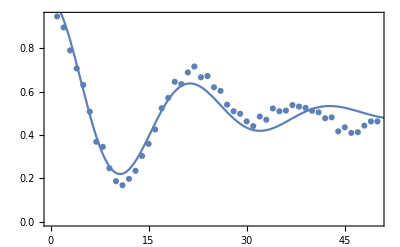

0.00262545

```mathematica
Pr5={0.9462890625,0.8955078125,0.7900390625,0.70703125,0.630859375,0.5078125,0.369140625,0.345703125,0.2470703125,0.1875,0.1689453125,0.1982421875,0.2353515625,0.3037109375,0.359375,0.42578125,0.5234375,0.5712890625,0.6455078125,0.634765625,0.6884765625,0.7158203125,0.666015625,0.671875,0.6201171875,0.603515625,0.5400390625,0.509765625,0.498046875,0.462890625,0.44140625,0.4853515625,0.470703125,0.5224609375,0.509765625,0.5126953125,0.5380859375,0.53125,0.525390625,0.51171875,0.5048828125,0.4775390625,0.4814453125,0.4169921875,0.435546875,0.41015625,0.4130859375,0.443359375,0.462890625,0.462890625};
PrN5=Table[{Ngates⟦i⟧,Pr5⟦i⟧},{i,50}];
FindFit[PrN5,f2,{c1,c2,c3,c4,T,T2},t]
fit5=NonlinearModelFit[PrN5,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN5],Plot[fit5[t],{t,0,60}],Frame->True]
fit5["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c1→0.518289,c2→0.448608,c3→-0.000678175,c4→-10.8691,T→39.0814,T2→42.617}

FittedModel[0.518289+0.448608 ⅇ^(«1») Cos[0.000678175+«19» t]]

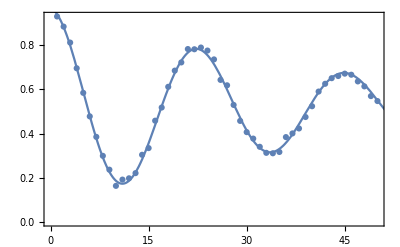

0.00016091

```mathematica
Pr7={0.9296875,0.8837890625,0.8115234375,0.6953125,0.583984375,0.4775390625,0.384765625,0.298828125,0.236328125,0.1630859375,0.19140625,0.197265625,0.220703125,0.3037109375,0.333984375,0.4580078125,0.517578125,0.611328125,0.6845703125,0.7216796875,0.7822265625,0.78125,0.7890625,0.775390625,0.7353515625,0.642578125,0.6181640625,0.529296875,0.45703125,0.40625,0.376953125,0.33984375,0.3125,0.310546875,0.31640625,0.3837890625,0.400390625,0.4228515625,0.474609375,0.5234375,0.58984375,0.625,0.650390625,0.66015625,0.6708984375,0.666015625,0.6357421875,0.61328125,0.5693359375,0.546875};
PrN7=Table[{Ngates⟦i⟧,Pr7⟦i⟧},{i,50}];
FindFit[PrN7,f2,{c1,c2,c3,c4,T,T2},t]
fit7=NonlinearModelFit[PrN7,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN7],Plot[fit7[t],{t,0,60}],Frame->True]
fit7["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

{c1→0.512394,c2→0.464858,c3→0.0304126,c4→1.28324,T→2.76676,T2→36.6815}

FittedModel[0.512394+0.464858 ⅇ^(«1») Cos[0.0304126+«19» t]]

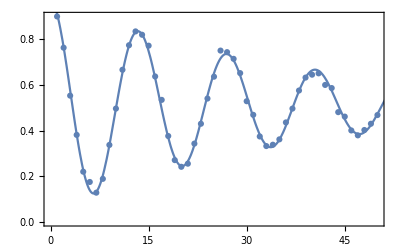

0.000211093

```mathematica
Pr8={0.8994140625,0.7626953125,0.552734375,0.380859375,0.2197265625,0.1748046875,0.1279296875,0.1884765625,0.3369140625,0.49609375,0.666015625,0.7734375,0.833984375,0.8193359375,0.771484375,0.63671875,0.5341796875,0.3759765625,0.2705078125,0.2412109375,0.2548828125,0.3427734375,0.4296875,0.5400390625,0.6357421875,0.75,0.7431640625,0.7138671875,0.6513671875,0.5283203125,0.46875,0.3740234375,0.33203125,0.337890625,0.361328125,0.435546875,0.49609375,0.5751953125,0.6318359375,0.64453125,0.650390625,0.599609375,0.5859375,0.48046875,0.4609375,0.400390625,0.37890625,0.40234375,0.4296875,0.4677734375};
PrN8=Table[{Ngates⟦i⟧,Pr8⟦i⟧},{i,50}];
FindFit[PrN8,f2,{c1,c2,c3,c4,T,T2},t]
fit8=NonlinearModelFit[PrN8,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN8],Plot[fit8[t],{t,0,60}],Frame->True]
fit8["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{c1→0.505692,c2→-0.333438,c3→3.70749,c4→-2.71362,T→4.29525,T2→22.2936}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[0.505692-0.333438 ⅇ^(«1») Cos[3.70749-«19» t]]

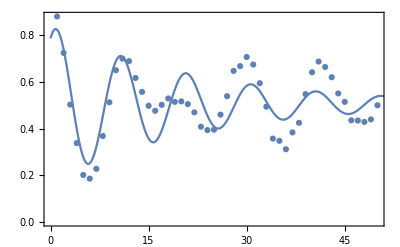

0.00781392

```mathematica
Pr9={0.880859375,0.724609375,0.5029296875,0.337890625,0.201171875,0.185546875,0.2275390625,0.3681640625,0.5126953125,0.650390625,0.7001953125,0.689453125,0.6171875,0.5576171875,0.498046875,0.4765625,0.501953125,0.529296875,0.5146484375,0.5166015625,0.5048828125,0.4697265625,0.408203125,0.3935546875,0.3955078125,0.4599609375,0.5390625,0.6474609375,0.66796875,0.70703125,0.6748046875,0.5947265625,0.494140625,0.357421875,0.34765625,0.3115234375,0.3837890625,0.4248046875,0.5478515625,0.6416015625,0.6875,0.6640625,0.6201171875,0.55078125,0.5146484375,0.435546875,0.4345703125,0.4287109375,0.439453125,0.5};
PrN9=Table[{Ngates⟦i⟧,Pr9⟦i⟧},{i,50}];
FindFit[PrN9,f2,{c1,c2,c3,c4,T,T2},t]
fit9=NonlinearModelFit[PrN9,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN9],Plot[fit9[t],{t,0,60}],Frame->True]
fit9["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

{c1→0.513964,c2→0.48563,c3→-0.0255648,c4→0.705768,T→1.1858,T2→26.2709}

FittedModel[0.513964+0.48563 ⅇ^(«1») Cos[0.0255648-«19» t]]

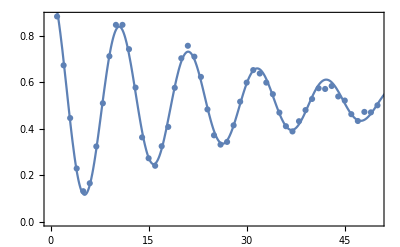

0.000244278

```mathematica
Pr10={0.8828125,0.6728515625,0.4462890625,0.2294921875,0.1318359375,0.166015625,0.32421875,0.509765625,0.7119140625,0.8466796875,0.8466796875,0.7421875,0.5771484375,0.36328125,0.2734375,0.2412109375,0.3251953125,0.408203125,0.576171875,0.703125,0.7568359375,0.7099609375,0.623046875,0.4833984375,0.3720703125,0.33203125,0.34375,0.4150390625,0.5166015625,0.5986328125,0.65234375,0.6376953125,0.5986328125,0.548828125,0.4697265625,0.4111328125,0.388671875,0.4326171875,0.48046875,0.5283203125,0.57421875,0.5712890625,0.583984375,0.5390625,0.521484375,0.462890625,0.43359375,0.47265625,0.470703125,0.5009765625};
PrN10=Table[{Ngates⟦i⟧,Pr10⟦i⟧},{i,50}];
FindFit[PrN10,f2,{c1,c2,c3,c4,T,T2},t]
fit10=NonlinearModelFit[PrN10,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN10],Plot[fit10[t],{t,0,60}],Frame->True]
fit10["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{c1→0.514364,c2→0.636364,c3→0.269056,c4→0.982685,T→1.67016,T2→7.37618}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.514364+0.636364 ⅇ^(«1») Cos[0.269056+«19» t]]

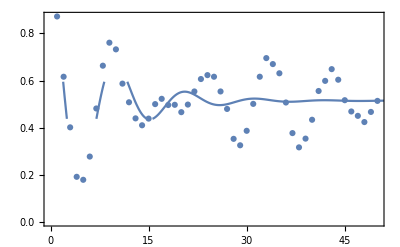

0.00793286

```mathematica
Pr11={0.8720703125,0.6162109375,0.4013671875,0.19140625,0.1787109375,0.27734375,0.4814453125,0.6630859375,0.7607421875,0.732421875,0.5869140625,0.5078125,0.439453125,0.41015625,0.4384765625,0.5,0.5224609375,0.49609375,0.4970703125,0.4658203125,0.498046875,0.5537109375,0.6064453125,0.623046875,0.6162109375,0.5537109375,0.4794921875,0.3525390625,0.3251953125,0.38671875,0.5009765625,0.6162109375,0.6953125,0.669921875,0.630859375,0.5068359375,0.376953125,0.31640625,0.353515625,0.43359375,0.5556640625,0.5986328125,0.6484375,0.603515625,0.5166015625,0.46875,0.4501953125,0.423828125,0.466796875,0.513671875};
PrN11=Table[{Ngates⟦i⟧,Pr11⟦i⟧},{i,50}];
FindFit[PrN11,f2,{c1,c2,c3,c4,T,T2},t]
fit11=NonlinearModelFit[PrN11,f2,{c1,c2,c4,c3,T2,T},t]
Show[ListPlot[PrN11],Plot[fit11[t],{t,0,60}],Frame->True]
fit11["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```